## Numerical Example (non-homog. b.c. for u and p):

```mathematica
lambda=0;
mu=1;
alpha=1;
c0=0;
K=IdentityMatrix[2];
```

### Displacement :

```mathematica
u[x_,y_,t_]:={x,y}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{0,y}

```mathematica
u[1,y,t]
```

{1,y}

```mathematica
u[x,0,t]
```

{x,0}

```mathematica
u[x,1,t]
```

{x,1}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

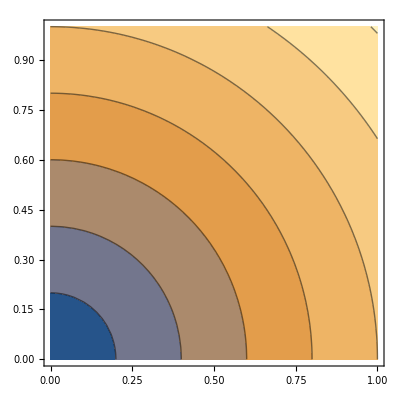

```mathematica
ContourPlot[Sqrt[(x)^2+(y)^2]/.t->0.001,{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_,t_]:= x
```

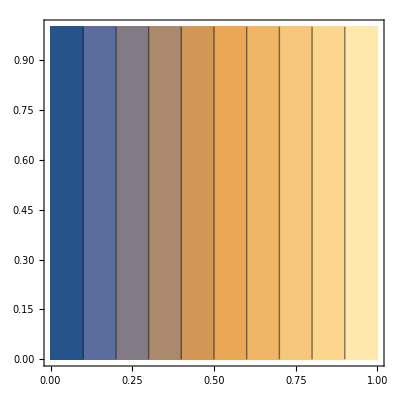

```mathematica
ContourPlot[p[x,y,t],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
{D[(x), x],D[(x), y]}//Simplify
```

{1,0}

```mathematica
{D[(y), x],D[(y), y]}//Simplify
```

{0,1}

```mathematica
Gradu[x_,y_,t_]:={{1,0},{0,1}}
```

Let us define ϵ (u) :

```mathematica
w=1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{1,0},{0,1}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
σe=2mu w+lambda Tr[w]IdentityMatrix[2]//Simplify
```

{{2,0},{0,2}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae[x_,y_,t_]:={{2,0},{0,2}}
```

### Stress:

```mathematica
Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

{{2-x,0},{0,2-x}}

```mathematica
Sigma[x_,y_,t_]:={{2-x,0},{0,2-x}}
```

ContourPlot of the Magnitude of the first row of σ :

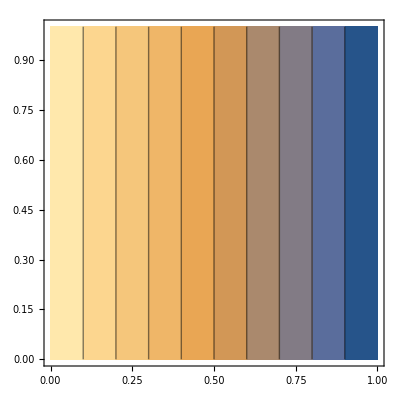

```mathematica
ContourPlot[2-x,{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

```mathematica
ContourPlot[2-x,{x,0,1},{y,0,1}]
```

-Graphics-

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

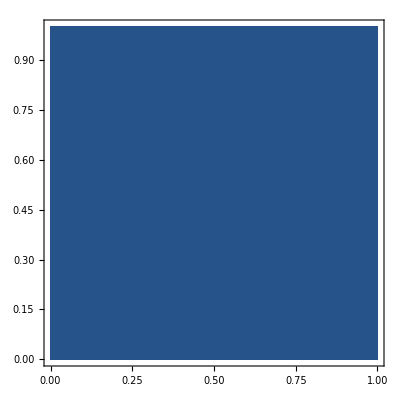

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
-K.{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{-1,0}

```mathematica
z[x_,y_,t_]:={-1,0}
```

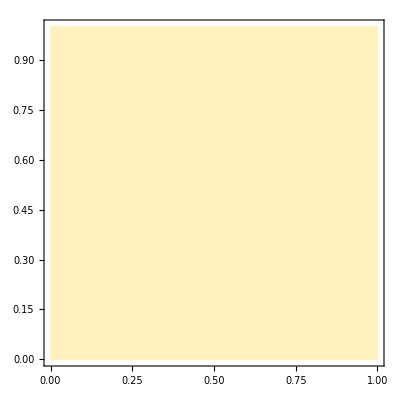

```mathematica
ContourPlot[1,{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{2-x,0},{0,2-x}}

```mathematica
-(D[2-x,x]+D[0,y])//Simplify
```

1

```mathematica
f1[x_,y_,t_]:=1
```

```mathematica
-(D[0,x]+D[2-x,y])//Simplify
```

0

```mathematica
f2[x_,y_,t_]:=0
```

### Source term q :

```mathematica
u[x,y,t]
```

{x,y}

```mathematica
z[x,y,t]
```

{-1,0}

```mathematica
D[c0 p[x,y,t]+alpha (D[x,x]+D[y,y]),t]+D[-1,x]+D[0,y]//Simplify
```

0

## Numerical Example (non-homog. b.c. for u and homog. b.c. for p):

```mathematica
lambda=0;
mu=1;
alpha=1;
c0=0;
K=IdentityMatrix[2];
```

### Displacement :

```mathematica
u[x_,y_,t_]:={x,y}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{0,y}

```mathematica
u[1,y,t]
```

{1,y}

```mathematica
u[x,0,t]
```

{x,0}

```mathematica
u[x,1,t]
```

{x,1}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

```mathematica
ContourPlot[Sqrt[(x)^2+(y)^2]/.t->0.001,{x,0,1},{y,0,1}]
```

-Graphics-

### Pressure:

```mathematica
p[x_,y_,t_]:= x(1-x)y(1-y)
```

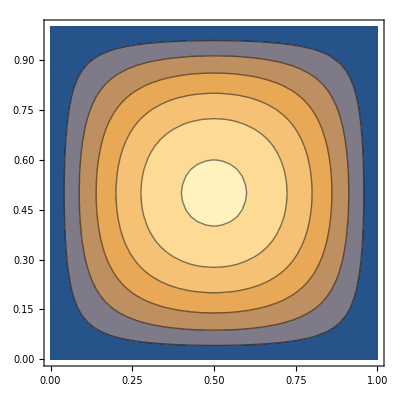

```mathematica
ContourPlot[p[x,y,t],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
{D[(x), x],D[(x), y]}//Simplify
```

{1,0}

```mathematica
{D[(y), x],D[(y), y]}//Simplify
```

{0,1}

```mathematica
Gradu[x_,y_,t_]:={{1,0},{0,1}}
```

Let us define ϵ (u) :

```mathematica
w=1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{1,0},{0,1}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
σe=2mu w+lambda Tr[w]IdentityMatrix[2]//Simplify
```

{{2,0},{0,2}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae[x_,y_,t_]:={{2,0},{0,2}}
```

### Stress:

```mathematica
Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

{{2-(-1+x) x (-1+y) y,0},{0,2-(-1+x) x (-1+y) y}}

```mathematica
Sigma[x_,y_,t_]:={{2-(-1+x) x (-1+y) y,0},{0,2-(-1+x) x (-1+y) y}}
```

ContourPlot of the Magnitude of the first row of σ :

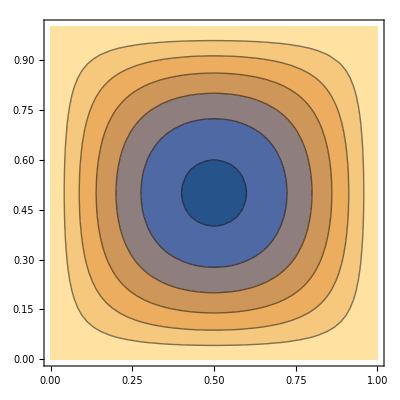

```mathematica
ContourPlot[2-(-1+x) x (-1+y) y,{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

```mathematica
ContourPlot[2-(-1+x) x (-1+y) y,{x,0,1},{y,0,1}]
```

-Graphics-

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

-Graphics-

### Darcy velocity :

```mathematica
-K.{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{y (-1-2 x (-1+y)+y),x (-1+x+2 y-2 x y)}

```mathematica
z[x_,y_,t_]:={y (-1-2 x (-1+y)+y),x (-1+x+2 y-2 x y)}
```

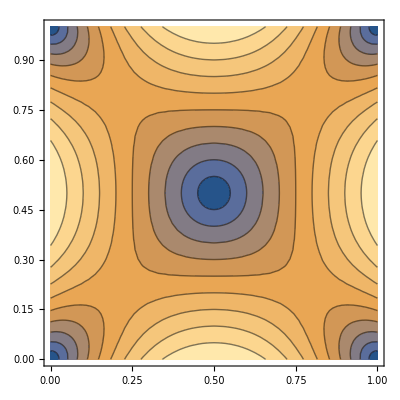

```mathematica
ContourPlot[Sqrt[(y (-1-2 x (-1+y)+y))^2+(x (-1+x+2 y-2 x y))^2],{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{2-(-1+x) x (-1+y) y,0},{0,2-(-1+x) x (-1+y) y}}

```mathematica
-(D[2-(-1+x) x (-1+y) y,x]+D[0,y])//Simplify
```

(-1+2 x) (-1+y) y

```mathematica
f1[x_,y_,t_]:=(-1+2 x) (-1+y) y
```

```mathematica
-(D[0,x]+D[2-(-1+x) x (-1+y) y,y])//Simplify
```

(-1+x) x (-1+2 y)

```mathematica
f2[x_,y_,t_]:=(-1+x) x (-1+2 y)
```

### Source term q :

```mathematica
u[x,y,t]
```

{x,y}

```mathematica
z[x,y,t]
```

{y (-1-2 x (-1+y)+y),x (-1+x+2 y-2 x y)}

```mathematica
D[c0 p[x,y,t]+alpha (D[x,x]+D[y,y]),t]+D[y (-1-2 x (-1+y)+y),x]+D[x (-1+x+2 y-2 x y),y]//Simplify
```

-2 (-1+x) x-2 (-1+y) y

```mathematica
q[x_,y_,t_]:=-2 (-1+x) x-2 (-1+y) y
```